# Friend Request Graph Generator

## Program that visualizes friend requests in a graph making it much easier to form teams.

## This was made by Willem Nielsen. Any issues please reach out to will@fastbreakkids.com and I will be happy to help

## Import Data

### Notes on required data structure

Your data must be in the form of a CSV file with two and only two columns, The names should be in the left column and the requests in the right. The requests can be delimited by commas or newlines. Any names that are misspelled will not register as the same person. I recommend you make the graph first and then correct the spelling in the view and edit your data section

### How to import

Upload your file to the wolfram cloud. Enter the file name in the quotes. To run a piece of code in this program you have to click it and press “Shift”+“Enter”.

```mathematica
friendRequestData = Import["/Users/erichegonzales/Downloads/4v4 Spring 24 Team Builder - M 3_4th Final Master Massaged.csv"];
```

## Data processing

```mathematica
requests =StringTrim[StringSplit[#, {",", "\n"}]]& /@ friendRequestData[[All, 2]];
```

```mathematica
names = friendRequestData[[All, 1]];
```

```mathematica
friendRequestDataCleaned = Transpose[{names,requests}];
```

## View and edit your data

To view and edit your data I recommend going back in the CSV that you uploaded and correcting any misspellings that you see. Then upload and run all cells again

## Graph your data

You can control the size of the graph with the number next to ImageSize. The vertices highlighted in red are people who were requested but not found in the names. Many of the red nodes are misspelled names.

I recommend looking through the red nodes and then editing your data in the spreadsheet above. Rinse repeat.

```mathematica
getEdges[req_]:= req[[1]]-> # & /@ req[[2]]
```

```mathematica
edges =Flatten[getEdges[#]&/@ friendRequestDataCleaned];
```

```mathematica
vertices = VertexList[edges];
notRegistered =Complement[vertices,names]
```

{,1)teddy kasell,aiden stern,alex moss,anyone from allen-stevenson or jack zegen,arin,beckett schein,ben ganfer,ben krawitz,ben moss,bobby vogulhut and harry trichon,carter,coach curtis team,coach mamadou if possible,coach shakeem,connor marcell,dalton 4th graders,david cunow,david dwek,dont put brothers together,elliot shalam,ethan adhoot,ethan s.,graham howard's group,henry bohm.,howie d,jacob bisselman,jacon b,jake henef,jake hennes,jake ibraham,jemal abraham,jeremiah o’connor,jonah,jon michael slattery,josh boucai,levi lichy,logan,makoto noguchi,maybe mix up the dalton kids?,maybe one 4th grader?,meijer butterman or jack zegan,n/as,nate and teddy kassel,nate kasell and jacob bisselman,nate kassel,nate kassell,nathan amar,needs to be with harry ahdoot and pierce ebrahimzadeh,niam,nico,noah,noah edelman,noah schankler,noah sky,patrick durkin,pax phillips,ramaz kids,riverdale boys,roark,roman,same as brother teddy,same team as the fall (rcs),sam waldron,teddy and nate kasell,teddy and nate kassel.,teddy defusco,teddy kassel,teddy kassell,teddy traxler and jackson sullivan,thomas smith,william gribbetz,will update,zach goldshmid,zach goldshmidt}

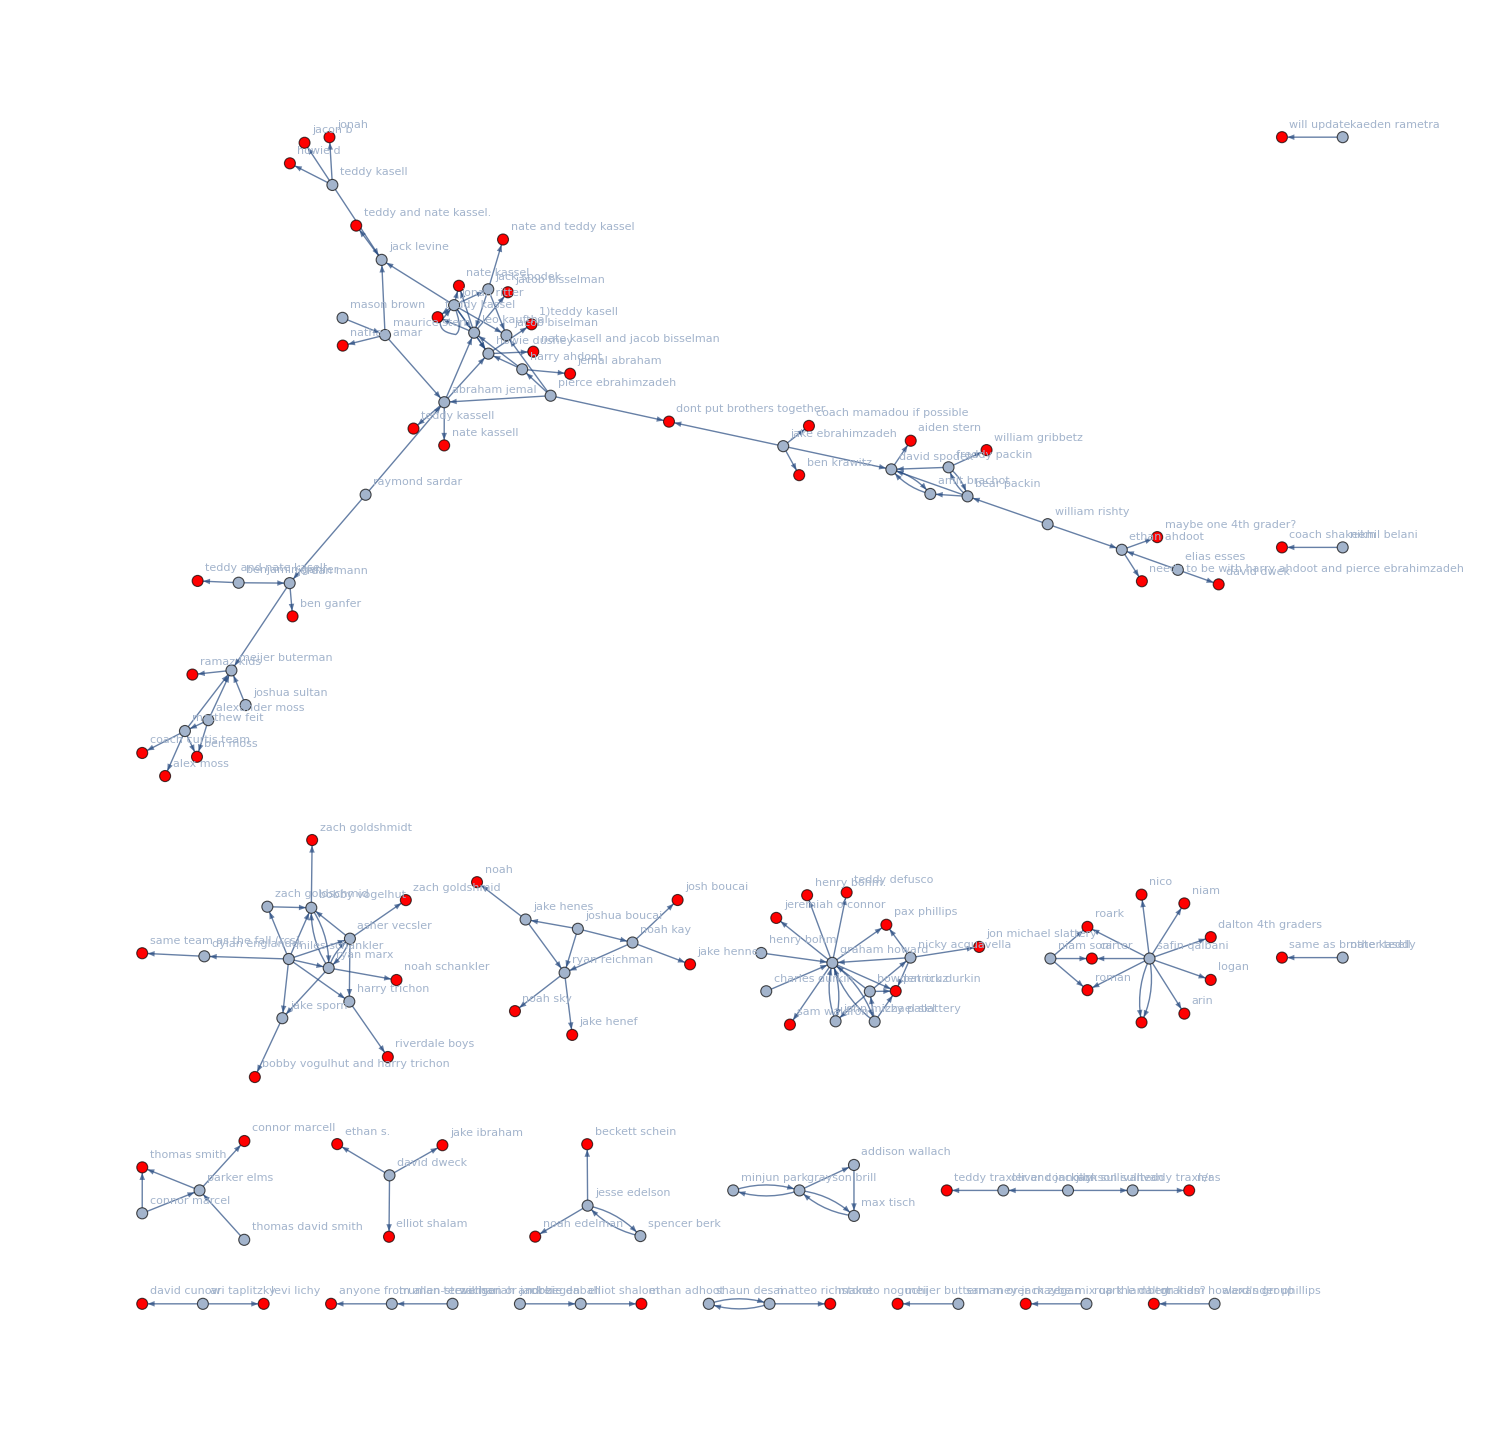

```mathematica
Graph[edges, VertexLabels->"Name",VertexStyle->Thread[notRegistered-> Red], ImageSize->1500]
```

### To save your graph right click it and select “save graphic”

Thanks for using! Again any issues please reach out to me either in person or at will@fastbreakkids.com.